```mathematica
Get["/Users/ethan.k/Desktop/CodingNStuff/Wolfram/Project/WindTunnel2DLBM/WindTunnel2DLBM.m"]
```

```mathematica
ex={1,1,0,-1,-1,-1,0,1,0};
ey={0,1,1,1,0,-1,-1,-1,0};
LBMDensityAndVelocity[f_]:=Block[{rho,u,v},rho=Total[f,{2}];
u=(f.ex)/rho;
v=(f.ey)/rho;
{rho,u,v}];
```

```mathematica
{1,1,0,-1,-1,-1,0,1,0}
```

{1,1,0,-1,-1,-1,0,1,0}

```mathematica
right={0,1};
left={0,-1};
bottom={1,0};
top={-1,0};
none={0,0};
streamDir={right,top+right,top,top+left,left,bottom+left,bottom,bottom+right,none};
LBMStream[f_]:=Transpose[MapThread[Flatten[RotateRight[#1,#2]]&,{f,streamDir}]];
```

```mathematica
{0,1}
```

{0,1}

```mathematica
wts={1/9,1/36,1/9,1/36,1/9,1/36,1/9,1/36,4/9};
LBMEquilibriumDistributions[rho_,u_,v_]:=Module[{uv,euv,velMag},uv=Transpose[{u,v}];
euv=uv.{ex,ey};
velMag=Transpose[ConstantArray[Total[uv^2,{2}],9]];
(Transpose[{rho}].{wts})*(1+3*euv+(9/2)*euv^2-(3/2)*velMag)];
```

```mathematica
{1/9,1/36,1/9,1/36,1/9,1/36,1/9,1/36,4/9}
```

{1/9,1/36,1/9,1/36,1/9,1/36,1/9,1/36,4/9}

```mathematica
Clear[f,feq,rho,ubc,vbc];
feq=LBMEquilibriumDistributions[{rho},{ubc},{vbc}][[1]];
eqn1=rho*ubc==Sum[ex[[i]]*f[i],{i,5}]+Sum[ex[[i]]*(feq[[i]]+wts[[i]]*(ex[[i]]*qx+ey[[i]]*qy)),{i,6,8}]+ex[[9]]*f[9];
eqn2=rho*vbc==Sum[ey[[i]]*f[i],{i,5}]+Sum[ey[[i]]*(feq[[i]]+wts[[i]]*(ey[[i]]*qx+ey[[i]]*qy)),{i,6,8}]+ey[[9]]*f[9];
eqn3=rho==Sum[f[i],{i,5}]+Sum[(feq[[i]]+wts[[i]]*(ey[[i]]*qx+ey[[i]]*qy)),{i,6,8}]+f[9];
res=FullSimplify[First[Solve[{eqn1,eqn2,eqn3},{rho,qx,qy}]]]
```

{rho→(f[1]+2 f[2]+2 f[3]+2 f[4]+f[5]+f[9])/(1+vbc),qx→1/(1+vbc)3 ((-6+5 ubc+3 (-2+ubc) vbc) f[1]+6 (-f[2]+f[4]+f[5])+6 vbc (-f[2]+f[4]+f[5])+ubc (5+3 vbc) (2 f[2]+2 f[3]+2 f[4]+f[5]+f[9])),qy→1/(1+vbc)((19+3 vbc (7+vbc)-3 ubc (5+3 vbc)) f[1]+14 f[2]-4 f[3]-22 f[4]-17 f[5]+f[9]-3 ubc (5+3 vbc) (2 f[2]+2 f[3]+2 f[4]+f[5]+f[9])+3 vbc (2 (3+vbc) f[2]-6 f[4]-5 f[5]+f[9]+vbc (2 f[3]+2 f[4]+f[5]+f[9])))}

```mathematica
Needs["WindTunnel2DLBM`"]
```

```mathematica
Get["WindTunnel2DLBM`"]
```

```mathematica
Rey=200;
charLen=1;
charVel=1;
ic=Function[{x,y},{0,0}];
state=WindTunnelInitialize[{Rey,charLen,charVel},ic,{x,0,6},{y,-1,1},t]
```

$Failed

```mathematica
Needs["WindTunnel2DLBM`"]
```

```mathematica
<<WindTunnel2DLBM`
```

```mathematica
FileNameJoin[{$UserBaseDirectory,"Applications"}]
```

/Users/ethan.k/Library/WolframDesktop/Applications

```mathematica
BeginPackage["WindTunnel2DLBM`"]
```

WindTunnel2DLBM`

```mathematica
Clear["Global`"]
```

```mathematica
<<WindTunnel2DLBM`
```

```mathematica
{}
```

{}

```mathematica
Rey=200;
charLen=1;
charVel=1;
ic=Function[{x,y},{0,0}];
state=WindTunnelInitialize[{Rey,charLen,charVel},ic,{x,0,6},{y,-1,1},t]
```

LBMState[<>]

```mathematica
<<"/Users/ethan.k/Desktop/CodingNStuff/Wolfram/WindTunnel2DLBM/WindTunnel2DLBM.m"
```

```mathematica
state["TimeStep"]
```

0.00333333

```mathematica
WindTunnelIterate[state,5];
state
```

LBMState[<0.,4.99667>]

```mathematica
{usol,vsol}={"U","V"}/. state[state["CurrentTime"]];
```

```mathematica
%19
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

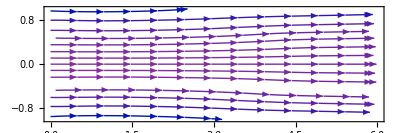

```mathematica
StreamPlot[{usol[x,y],vsol[x,y]},{x,0,6},{y,-1,1},AspectRatio->Automatic,ImageSize->400,PlotRangePadding->None]
```

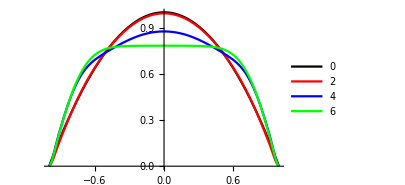

```mathematica
Plot[Evaluate[{usol[#,y]&/@Range[0,6,2]}],{y,-1,1},ImageSize->300,PlotLegends->Range[0,6,2],PlotStyle->{Black,Red,Blue,Green}]
```

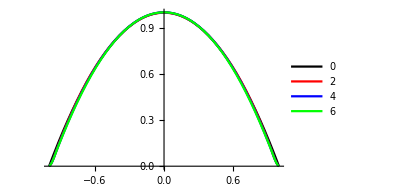

```mathematica
WindTunnelIterate[state,20];
{usol,vsol}={"U","V"}/. state[state["CurrentTime"]];
Plot[Evaluate[{usol[#,y]&/@Range[0,6,2]}],{y,-1,1},ImageSize->300,PlotLegends->Range[0,6,2],PlotStyle->{Black,Red,Blue,Green}]
```

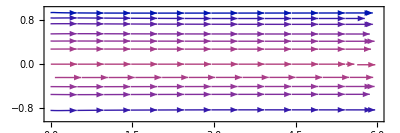

```mathematica
StreamPlot[{usol[x,y],vsol[x,y]},{x,0,6},{y,-1,1},AspectRatio->Automatic,ImageSize->400,PlotRangePadding->None]
```

```mathematica
Remove[state];
state=WindTunnelInitialize[{200,1,1},Function[{x,y},{0,0}],{x,0,15},{y,-2,2},t,"CharacteristicLatticePoints"->15,"ObjectsInTunnel"->{ParametricRegion[{3+Cos[s]/2,Sin[s]/2},{{s,0,2 Pi}}]}]
```

LBMState[<>]

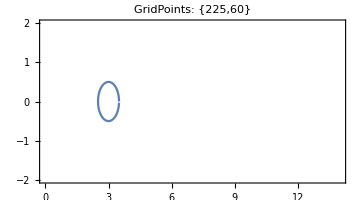

```mathematica
ListLinePlot[state["ObjectsInTunnel"],PlotRange->{{0,14},{-2,2}},AspectRatio->Automatic,Axes->False,Frame->True,ImageSize->Medium,PlotLabel->StringForm["GridPoints: ``",Reverse@state["GridPoints"]]]
```

```mathematica
WindTunnelIterate[state,10];
{usol,vsol}={"U","V"}/. state[state["CurrentTime"]];

Rasterize@Show[LineIntegralConvolutionPlot[{{usol[x,y],vsol[x,y]},{"noise",300,400}},{x,0,15},{y,-2,2},AspectRatio->Automatic,ImageSize->Medium,PlotRangePadding->None,LineIntegralConvolutionScale->2,ColorFunction->"RoseColors"],ListLinePlot[state["ObjectsInTunnel"],PlotStyle->{{Thickness[0.005],Black}}]]
```

-Graphics-

```mathematica
WindTunnelIterate[state,30];
{usol,vsol}={"U","V"}/. state[state["CurrentTime"]];
```

```mathematica
cc=N@Range[-3,3,4/100];
cc=DeleteCases[cc,x_/;-0.4<=x<=0.4];
cname="VisibleSpectrum";
cdata=ColorData[cname];
crange=ColorData[cname,"Range"];
cMinMax={Min[cc],Max[cc]};
colors=cdata[Rescale[#,cMinMax,crange]]&/@cc;
```

```mathematica
Remove[vort];
vort=D[usol[x,y],y]-D[vsol[x,y],x];
Rasterize@Show[ContourPlot[vort,{x,0,15},{y,-2,2},AspectRatio->Automatic,ImageSize->500,Contours->cc,ContourShading->None,ContourStyle->colors,PlotRange->{{0,15},{-2,2},All}],Graphics[Polygon[state["ObjectsInTunnel"]]]]
```

```mathematica
state=WindTunnelInitialize[{200,1,1},Function[{x,y},{0,0}],{x,0,15},{y,-2,2},t,"CharacteristicLatticePoints"->15,"ObjectsInTunnel"->{ParametricRegion[{3+Cos[s]/2,Sin[s]/2},{{s,0,2 Pi}}]}];
```

```mathematica
cc=N@Range[-5,5,10/200];
cc=DeleteCases[cc,x_/;-0.5<=x<=0.5];
cname="VisibleSpectrum";
cdata=ColorData[cname];
crange=ColorData[cname,"Range"];
cMinMax={Min[cc],Max[cc]};
colors=cdata[Rescale[#,cMinMax,crange]]&/@cc;

res=Table[WindTunnelIterate[state,t];
{usol,vsol}={"U","V"}/. state[state["CurrentTime"]];
vort=D[usol[x,y],y]-D[vsol[x,y],x];
plot=Show[ContourPlot[vort,{x,0,15},{y,-2,2},AspectRatio->Automatic,ImageSize->Medium,Contours->cc,ContourShading->None,ContourStyle->colors,PlotRange->{{0,15},{-2,2},All}],Graphics[Point/@state["ObjectsInTunnel"]]];
Rasterize[plot],{t,0,50,1}];
```

```mathematica
ListAnimate[res,DefaultDuration->10,AnimationRunning->False]
```

```mathematica
Remove[state];
inletVel=Fit[{{7/10,0},{17/20,1},{1,0}},{1,x,x^2},x];
state=WindTunnelInitialize[{500,0.3,1},Function[{x,y},{0,0}],{x,-1.1,1.1},{y,0,1.1},t,"CharacteristicLatticePoints"->20,"TunnelBoundaryConditions"->{"Left"->"NoSlip","Right"->"NoSlip","Top"->"NoSlip","Bottom"->Function@@List[{x,y,t},If@@List[0.7<=x<=1.,{0,inletVel},If[-1<=x<=-0.7,"Outflow",{0,0}]]]},"ObjectsInTunnel"->{ImplicitRegion[0.7<=(x^4+y^4)^(1/4)<=1,{{x,-1,1},{y,-0.2,1}}],ParametricRegion[{0.22+t,t-0.2},{{t,0.55,0.7}}]}]
```

LBMState[<>]

```mathematica
ProgressIndicator[Dynamic[state["CurrentTime"]],{0,40}]
AbsoluteTiming[WindTunnelIterate[state,40]]
```

{141.252,Null}

```mathematica
{usol,vsol}={"U","V"}/. state[state["CurrentTime"]];
vort=D[usol[x,y],y]-D[vsol[x,y],x];
cc=N@Range[-20,20,40/50];
cc=DeleteCases[cc,x_/;-0.1<=x<=0.1];
cname="VisibleSpectrum";
cdata=ColorData[cname];
crange=ColorData[cname,"Range"];
cMinMax={Min[cc],Max[cc]};
colors=cdata[Rescale[#,cMinMax,crange]]&/@cc;
Rasterize@Show[ContourPlot[vort,{x,-1,1},{y,0,1},AspectRatio->Automatic,ImageSize->Medium,Contours->cc,ContourShading->None,ContourStyle->colors,PlotRange->{{-1,1},{0,1},All},RegionFunction->Function[{x,y},0.7<=(x^4+y^4)^(1/4)<=1]],Graphics[Point/@state["ObjectsInTunnel"]]]
```

-Graphics-

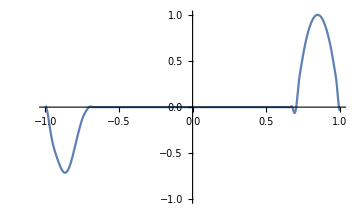

```mathematica
Plot[vsol[x,0],{x,-1,1},PlotRange->{{-1,1},{-1,1}},ImageSize->Medium]
```

```mathematica
Clear[mat,a,b,t,AOA];
Manipulate[mat={{Cos[(AOA-30) Degree],-Sin[(AOA-30) Degree]},{Sin[(AOA-30) Degree],Cos[(AOA-30) Degree]}};
ParametricPlot[mat.{1.5t^2,0.4 ((t^2-0.25t^4)/b)},{t,-1,1},AspectRatio->Automatic,ImageSize->Medium,PlotRange->{{0,2},{-0.4,0.1}}],{{b,0.9},0.1,10},{{AOA,0,"Angle of Attack"},-45,45}]
```

```mathematica
Clear[mat,pts,a,b,t,AOA];
Manipulate[pts={{0,0},{100,a},{160,b},{194,0}};
mat={{Cos[(AOA) Degree],-Sin[(AOA) Degree]},{Sin[(AOA) Degree],Cos[(AOA) Degree]}};
f=BezierFunction[pts];
ParametricPlot[mat.{f[t][[1]],f[t][[2]]},{t,0,1},AspectRatio->Automatic,ImageSize->Medium,PlotRange->{{0,250},{-15,50}}],{{a,0.9},0.1,20},{{b,0.9},0.1,20},{{AOA,0,"Angle of Attack"},-45,45},Dynamic[NIntegrate[Sqrt[Power[D[3((1−t)^2)t*100+3(1−t)(t^2)160+(t^3)*194,t],2]+Power[D[3((1−t)^2)t*a+3(1−t)(t^2)*b,t],2]],{t,0,1}]]]
```

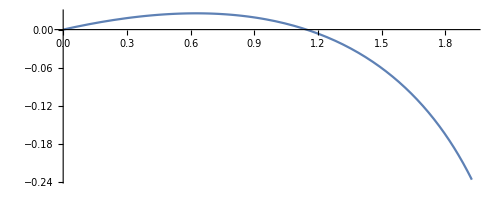

```mathematica
ParametricPlot[{0.01*{Cos[-7Degree],-Sin[-7Degree]},0.01*{Sin[-7Degree],Cos[-7Degree]}}.{3((1−t)^2)t*100+3(1−t)(t^2)160+(t^3)*194,3((1−t)^2)t*20+3(1−t)(t^2)*17.3},{t,0,1}]
```

```mathematica
NIntegrate[Sqrt[Power[D[3((1−t)^2)t*100+3(1−t)(t^2)160,t],2]+Power[D[3((1−t)^2)t*10+3(1−t)(t^2)*10,t],2]],{t,0,1}]
```

198.158

```mathematica
ClearAll[t]
D[3 ((1-t)^2) t*100+3 (1-t) (t^2) 160,t]
```

300 (1-t)^2+360 (1-t) t-480 t^2

```mathematica
sail=Interpolation[{{0,0},{0.38443,0.015485},{0.69828,0.0045},{0.9528,-0.037},{1.16905,-0.094},{1.3887,-0.15374},{1.5,-0.2095}}]
```

```mathematica
InterpolatingFunction[…]
```

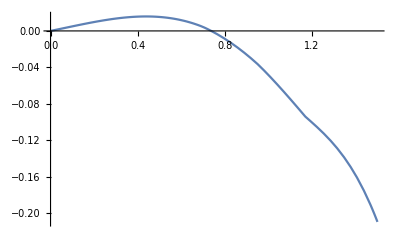

InterpolatingFunction[…]

```mathematica
Plot[sail[x],{x,0,1.5}]
```

```mathematica
?RefLink
```

```mathematica
Plot[sail[x],{x,0,1.5}]
```

-Graphics-

ListLinePlot::lpn: LBMState[<0.,9.99833>][ParametricRegion[{{0.111469 (Times[«3»]+Times[«3»])+0.993768 (Times[«3»]+Times[«3»]),0.993768 (Times[«3»]+Times[«3»])-0.111469 (Times[«3»]+Times[«3»])},0.≤t≤1.},{t}]] is not a list of numbers or pairs of numbers.

ListLinePlot[LBMState[<0.,9.99833>][ParametricRegion[{{0.111469 (35.64 (1-t)^2 t+60 (1-t) t^2)+0.993768 (300 (1-t)^2 t+480 (1-t) t^2),0.993768 (35.64 (1-t)^2 t+60 (1-t) t^2)-0.111469 (300 (1-t)^2 t+480 (1-t) t^2)},0≤t≤1},{t}]],PlotRange→{{-2,6},{-1,1}}]

```mathematica
Clear[a,b,t,AOA];
Manipulate[mat={{Cos[AOA Degree],-Sin[AOA Degree]},{Sin[AOA Degree],Cos[AOA Degree]}};
ParametricPlot[mat.{1.5t^2,0.2 (t-t^3+(t^2-t^4)/b)/a},{t,-1,1},AspectRatio->Automatic,ImageSize->Medium,PlotRange->{{0,2},{-1,1}}],{{a,1},0.1,10},{{b,0.9},0.3,10},{{AOA,0,"Angle of Attack"},-20,20}]
```

```mathematica
Clear[jmat,jpts,ja,jb,jt,jAOA];
Manipulate[jpts={{0,0},{50,ja},{165,jb}};
jmat={{Cos[(jAOA) Degree],-Sin[(jAOA) Degree]},{Sin[(jAOA) Degree],Cos[(jAOA) Degree]}};
jf=BezierFunction[jpts];
ParametricPlot[jmat.{jf[jt][[1]],jf[jt][[2]]},{jt,0,1},AspectRatio->Automatic,ImageSize->Medium,PlotRange->{{0,200},{-45,40}}],{{ja,0.9},0.1,50},{{jb,0.9},0.1,50},{{jAOA,0,"Angle of Attack"},-45,45},Dynamic[NIntegrate[Sqrt[Power[D[2(1−jt)jt*50+(jt^2)*165,jt],2]+Power[D[2(1−jt)jt*ja+(jt^2)*jb,jt],2]],{jt,0,1}]]]
```

```mathematica
Clear[mat,pts,a,b,t,AOA];
Manipulate[pts={{0,0},{50,a},{150,b},{194,0}};
mat={{Cos[(AOA) Degree],-Sin[(AOA) Degree]},{Sin[(AOA) Degree],Cos[(AOA) Degree]}};
f=BezierFunction[pts];
ParametricPlot[mat.{f[t][[1]],f[t][[2]]},{t,0,1},AspectRatio->Automatic,ImageSize->Medium,PlotRange->{{0,250},{-35,30}}],{{a,0.9},0.1,50},{{b,0.9},0.1,50},{{AOA,0,"Angle of Attack"},-45,45},Dynamic[NIntegrate[Sqrt[Power[D[3((1−t)^2)t*50+3(1−t)(t^2)150+(t^3)*194,t],2]+Power[D[3((1−t)^2)t*a+3(1−t)(t^2)*b,t],2]],{t,0,1}]]]
```

Lattice velocity = windpseed lower = slower
0.5773502692 lattice velocity = 666.739kts
0.01=11.55kts
0.0008658008658 per kts

```mathematica
$Path
```

{/Users/ethan.k/Library/WolframDesktop/DocumentationIndices,/Applications/Wolfram Desktop.app/Contents/SystemFiles/Links,/Users/ethan.k/Library/WolframDesktop/Kernel,/Users/ethan.k/Library/WolframDesktop/Autoload,/Users/ethan.k/Library/WolframDesktop/Applications,/Library/WolframDesktop/Kernel,/Library/WolframDesktop/Autoload,/Library/WolframDesktop/Applications,.,/Users/ethan.k,/Applications/Wolfram Desktop.app/Contents/AddOns/Packages,/Applications/Wolfram Desktop.app/Contents/SystemFiles/Autoload,/Applications/Wolfram Desktop.app/Contents/AddOns/Autoload,/Applications/Wolfram Desktop.app/Contents/AddOns/Applications,/Applications/Wolfram Desktop.app/Contents/AddOns/ExtraPackages,/Applications/Wolfram Desktop.app/Contents/SystemFiles/Kernel/Packages,/Applications/Wolfram Desktop.app/Contents/Documentation/English/System,/Applications/Wolfram Desktop.app/Contents/SystemFiles/Data/ICC}

```mathematica
Table[n,{n,0.004329004329,0.017316017316,0.0008658008658}]
```

{0.004329,0.00519481,0.00606061,0.00692641,0.00779221,0.00865801,0.00952381,0.0103896,0.0112554,0.0121212,0.012987,0.0138528,0.0147186,0.0155844,0.0164502,0.017316}

```mathematica
sAngle=5;
bAngle=50;
wind=20*0.0008658008658;
state=WindTunnelInitialize[{375,1,0.5},Function[{x,y},{0,0}],{x,-4,6},{y,-2.5,2},t,"CharacteristicLatticePoints"->20,"CharacteristicLatticeVelocity"->wind,"TunnelBoundaryConditions"->{"Left"->Function[{x,y,t},{1,0}],"Right"->"Outflow","Top"->"Periodic"},"ObjectsInTunnel"->{ParametricRegion[{0.01{Cos[(-bAngle+sAngle)Degree],-Sin[(-bAngle+sAngle)Degree]},0.01*{Sin[(-bAngle+sAngle)Degree],Cos[(-bAngle+sAngle)Degree]}}.{3((1−t)^2)t*50+3(1−t)(t^2)150+(t^3)*194,3((1−t)^2)t*20+3(1−t)(t^2)*30},{{t,0,1}}],ParametricRegion[{0.01{Cos[(-bAngle+sAngle+10)Degree],-Sin[(-bAngle+sAngle+10)Degree]},0.01*{Sin[(-bAngle+sAngle+10)Degree],Cos[(-bAngle+sAngle+10)Degree]}}.{2(1−jt)jt*50+(jt^2)*163,2(1−jt)jt*35+(jt^2)*32.5}+{-Cos[(bAngle)Degree]*(183*0.01),Sin[(bAngle)Degree]*(183*0.01)},{{jt,0,1}}]}];
```

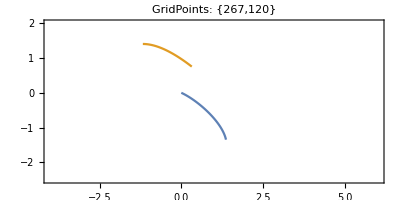

```mathematica
ListLinePlot[state["ObjectsInTunnel"],PlotRange->Evaluate[state["Ranges"]],AspectRatio->Automatic,Axes->False,Frame->True,ImageSize->400,PlotLabel->StringForm["GridPoints: ``",Reverse@state["GridPoints"]]]
```

```mathematica
10/state["TimeStep"]
```

5775.

```mathematica
ProgressIndicator[Dynamic[state["CurrentTime"]],{0,10}]
AbsoluteTiming[WindTunnelIterate[state,10]]
```

{77.9442,Null}

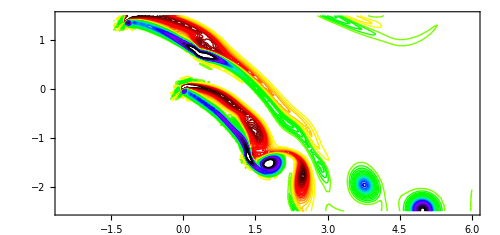

```mathematica
{usol,vsol}={"U","V"}/. state[state["CurrentTime"]];
vort=D[usol[x,y],y]-D[vsol[x,y],x];
cc=N@Range[-15,15,30/60];
cc=DeleteCases[cc,x_/;-0.1<=x<=0.1];
cname="VisibleSpectrum";
cdata=ColorData[cname];
crange=ColorData[cname,"Range"];
cMinMax={Min[cc],Max[cc]};
colors=cdata[Rescale[#,cMinMax,crange]]&/@cc;
Show[ContourPlot[vort,{x,-2.5,6},{y,-2.5,1.5},AspectRatio->Automatic,ImageSize->500,Contours->cc,ContourShading->None,ContourStyle->colors,PlotRange->{{-2.5,6},{-2.5,1.5},All}],Graphics[{FaceForm[White],EdgeForm[Black]}]]
```

```mathematica
PressureCoefficient[x_?NumericQ,y_?NumericQ]:=(psol[x,y]-psol[-3.5,0])/(0.5*state["InternalVelocity"]^2)
```

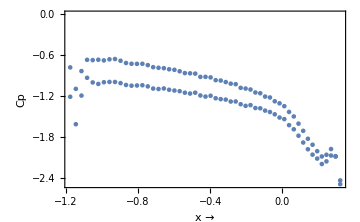

0.321445

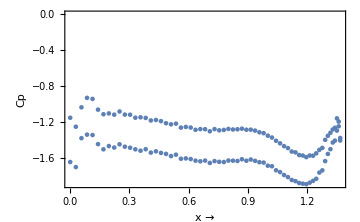

0.344616

```mathematica
jobjs=Join[Reverse[state["ObjectsInTunnel"][[2]]],Map[Plus[#,{0,0.01}]&,state["ObjectsInTunnel"][[2]]]];
jpsol="P"/. state[state["CurrentTime"]];
jpp=Apply[jpsol,jobjs,1];
jpp=(jpp-jpsol[-3.5,0])/(0.5*state["InternalVelocity"]^2);
ListPlot[Transpose[{jobjs[[All,1]],jpp}],PlotRange->All,Axes->False,Frame->True,FrameLabel->{"x →","Cp"},FrameStyle->Directive[Black,14],ImageSize->Medium]
jCl=Subtract[Drop[#,1]&/@GatherBy[Transpose[{jobjs[[All,1]],jpp}],First][[43]][[1]][[2]],Drop[#,1]&/@GatherBy[Transpose[{jobjs[[All,1]],jpp}],First][[43]][[2]][[2]]]

objs=Join[Reverse[state["ObjectsInTunnel"][[1]]],Map[Plus[#,{0,0.01}]&,state["ObjectsInTunnel"][[1]]]];
psol="P"/. state[state["CurrentTime"]];
pp=Apply[psol,objs,1];
pp=(pp-psol[-3.5,0])/(0.5*state["InternalVelocity"]^2);
ListPlot[Transpose[{objs[[All,1]],pp}],PlotRange->All,Axes->False,Frame->True,FrameLabel->{"x →","Cp"},FrameStyle->Directive[Black,14],ImageSize->Medium]
Cl=Subtract[Drop[#,1]&/@GatherBy[Transpose[{objs[[All,1]],pp}],First][[40]][[1]][[2]],Drop[#,1]&/@GatherBy[Transpose[{objs[[All,1]],pp}],First][[40]][[2]][[2]]]
```

```mathematica
jL=jCl*3.7379459869*0.5*712*(20/1.94384)^2;
mL=Cl*8.6730190131*0.5*712*(20/1.94384)^2;
L=mL+jL;
{wind,-bAngle,L}
```

{0.017316,-50,157923.}

```mathematica
Drop[#,1]&/@Cases[Transpose[{objs[[All,1]],pp}],{x_,y_}/;0.605<x<0.645][[1]][[2]]
```

-0.787843

```mathematica
Drop[#,1]&/@Cases[Transpose[{objs[[All,1]],pp}],{x_,y_}/;0.605<x<0.645][[2]][[2]]
```

-1.03238

```mathematica
Cases[Transpose[{objs[[All,1]],pp}],{x_,y_}/;0.605<x<0.640]
```

{{0.634274,-1.28813},{0.609791,-1.2627},{0.609791,-1.61469},{0.634274,-1.63275}}

{{-0.852116,-0.371875},{-0.852116,-0.602496}}

-1

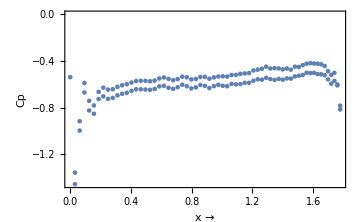

```mathematica
Cases[Transpose[{jobjs[[All,1]],jpp}],{x_,y_}/;-0.875<x<-0.845]
```

```mathematica
Mag[s_,b_,w_]:=Module[{sAngle=s,bAngle=b,wind=w*0.0008658008658},
state=WindTunnelInitialize[{375,0.75,0.4},Function[{x,y},{0,0}],{x,-4,6},{y,-2.5,2},t,"CharacteristicLatticePoints"->20,"CharacteristicLatticeVelocity"->wind,"TunnelBoundaryConditions"->{"Left"->Function[{x,y,t},{1,0}],"Right"->"Outflow","Top"->"Periodic"},"ObjectsInTunnel"->{ParametricRegion[{0.01{Cos[(-bAngle+sAngle)Degree],-Sin[(-bAngle+sAngle)Degree]},0.01*{Sin[(-bAngle+sAngle)Degree],Cos[(-bAngle+sAngle)Degree]}}.{3((1−t)^2)t*50+3(1−t)(t^2)150+(t^3)*194,3((1−t)^2)t*20+3(1−t)(t^2)*30},{{t,0,1}}],ParametricRegion[{0.01{Cos[(-bAngle+sAngle+10)Degree],-Sin[(-bAngle+sAngle+10)Degree]},0.01*{Sin[(-bAngle+sAngle+10)Degree],Cos[(-bAngle+sAngle+10)Degree]}}.{2(1−jt)jt*50+(jt^2)*165,2(1−jt)jt*30+(jt^2)*25}+{-Cos[(bAngle)Degree]*(183*0.01),Sin[(bAngle)Degree]*(183*0.01)},{{jt,0,1}}]}];

AbsoluteTiming[WindTunnelIterate[state,10]];

{usol,vsol}={"U","V"}/. state[state["CurrentTime"]];
vort=D[usol[x,y],y]-D[vsol[x,y],x];
cc=N@Range[-15,15,30/60];
cc=DeleteCases[cc,x_/;-0.1<=x<=0.1];
cname="VisibleSpectrum";
cdata=ColorData[cname];
crange=ColorData[cname,"Range"];
cMinMax={Min[cc],Max[cc]};
colors=cdata[Rescale[#,cMinMax,crange]]&/@cc;
Show[ContourPlot[vort,{x,-2.5,6},{y,-2.5,1.5},AspectRatio->Automatic,ImageSize->500,Contours->cc,ContourShading->None,ContourStyle->colors,PlotRange->{{-2.5,6},{-2.5,1.5},All}]]

jobjs=Join[Reverse[state["ObjectsInTunnel"][[2]]],Drop[Map[Plus[#,{0,0.01}]&,state["ObjectsInTunnel"][[2]]],1]];
jpsol="P"/. state[state["CurrentTime"]];
jpp=Apply[jpsol,jobjs,1];
jpp=(jpp-jpsol[-3.5,0])/(0.5*state["InternalVelocity"]^2);
jCl=Subtract[Drop[#,1]&/@Cases[Transpose[{jobjs[[All,1]],jpp}],{x_,y_}/;-1.599<x<-1.596][[1]][[2]],Drop[#,1]&/@Cases[Transpose[{jobjs[[All,1]],jpp}],{x_,y_}/;-1.599<x<-1.596][[2]][[2]]];

objs=Join[Reverse[state["ObjectsInTunnel"][[1]]],Drop[Map[Plus[#,{0,0.01}]&,state["ObjectsInTunnel"][[1]]],1]];
psol="P"/. state[state["CurrentTime"]];
pp=Apply[psol,objs,1];
pp=(pp-psol[-3.5,0])/(0.5*state["InternalVelocity"]^2);
Cl=Subtract[Drop[#,1]&/@Cases[Transpose[{objs[[All,1]],pp}],{x_,y_}/;0.248<x<0.250][[1]][[2]],Drop[#,1]&/@Cases[Transpose[{objs[[All,1]],pp}],{x_,y_}/;0.248<x<0.250][[2]][[2]]];

jL=jCl*3.7379459869*0.5*712*w^2;
mL=Cl*8.6730190131*0.5*712*w^2;
L=mL+jL;
{wind,-bAngle,L}
]
```

```mathematica
Mag[2.5,22.5,11]
```

Set::write: Tag Times in  {{-0.0567831,0.371762},{-0.0856826,0.383652},{-0.114628,0.39543},{-0.14362,0.407093},«3»,{-0.260069,0.452527},{-0.289305,0.463564},{-0.318592,0.474466},«99»} is Protected.

{0.00952381,-22.5,53549.2}

```mathematica
Cases[Transpose[{jobjs[[All,1]],jpp}],{x_,y_}/;-1.599<x<-1.596]
```

{}

```mathematica
Cases[Transpose[{jobjs[[All,1]],jpp}],{-1.5975029942860937,___}]
```

{{-1.5975,-0.367738},{-1.5975,-0.435286}}

```mathematica
Subtract[Drop[#,1]&/@GatherBy[Transpose[{jobjs[[All,1]],jpp}],First][[43]][[1]][[2]],Drop[#,1]&/@GatherBy[Transpose[{jobjs[[All,1]],jpp}],First][[43]][[2]][[2]]]
```

0.321445

```mathematica
GatherBy[Transpose[{objs[[All,1]],pp}],First][[40]]
```

{{0.634274,-1.28813},{0.634274,-1.63275}}

```mathematica
state["ObjectsInTunnel"][[1]]
```

{{0.,0.},{0.0312421,-0.000683694},{0.0624665,-0.00193657},{0.0936658,-0.00371134},{0.124834,-0.00596854},{0.155966,-0.00867487},{0.187059,-0.0118021},{0.21811,-0.015326},{0.249115,-0.0192259},{0.280073,-0.0234839},{0.310983,-0.0280845},{0.341841,-0.0330144},{0.372648,-0.0382618},{0.4034,-0.0438166},{0.434096,-0.0496703},{0.464736,-0.0558151},{0.495318,-0.0622447},{0.525839,-0.0689534},{0.556299,-0.0759367},{0.586695,-0.0831907},{0.617026,-0.0907122},{0.64729,-0.0984988},{0.677486,-0.106549},{0.70761,-0.11486},{0.737661,-0.123434},{0.767636,-0.132268},{0.797533,-0.141364},{0.827348,-0.150722},{0.85708,-0.160345},{0.886724,-0.170233},{0.916278,-0.180389},{0.945736,-0.190817},{0.975097,-0.201519},{1.00435,-0.212499},{1.0335,-0.223763},{1.06254,-0.235315},{1.09146,-0.24716},{1.12025,-0.259305},{1.14891,-0.271756},{1.17744,-0.284522},{1.20581,-0.29761},{1.23404,-0.311029},{1.26209,-0.324788},{1.28998,-0.338899},{1.31767,-0.353373},{1.34517,-0.368221},{1.37245,-0.383458},{1.39951,-0.399098},{1.42631,-0.415156},{1.45286,-0.431649},{1.47911,-0.448595},{1.50506,-0.466014},{1.53066,-0.483926},{1.5559,-0.502354},{1.58074,-0.521321},{1.60513,-0.540853},{1.62904,-0.560977},{1.65241,-0.581721},{1.67519,-0.603114},{1.69731,-0.625185},{1.7187,-0.647965},{1.73927,-0.671482},{1.75894,-0.695763},{1.7776,-0.720832}}

```mathematica
Subtract[Drop[#,1]&/@GatherBy[Transpose[{objs[[All,1]],pp}],First][[43]][[1]][[2]],Drop[#,1]&/@GatherBy[Transpose[{objs[[All,1]],pp}],First][[43]][[2]][[2]]]
```

0.34783

```mathematica
GatherBy[Transpose[{jobjs[[All,1]],jpp}],First]
```

{{{0.211418,-2.20034},{0.211418,-2.22562}},{{0.187006,-1.93913},{0.187006,-2.0333}},{{0.162495,-1.90445},{0.162495,-2.07862}},{{0.137884,-2.02769},{0.137884,-2.22002}},{{0.113169,-2.0512},{0.113169,-2.23584}},{{0.0883506,-1.96731},{0.0883506,-2.16792}},{{0.0634252,-1.90524},{0.0634252,-2.11195}},{{0.0383913,-1.79789},{0.0383913,-2.01575}},{{0.0132469,-1.69487},{0.0132469,-1.91826}},{{-0.0120101,-1.59439},{-0.0120101,-1.83622}},{{-0.0373817,-1.51234},{-0.0373817,-1.75941}},{{-0.0628702,-1.40274},{-0.0628702,-1.65687}},{{-0.0884777,-1.35299},{-0.0884777,-1.62154}},{{-0.114206,-1.29934},{-0.114206,-1.55656}},{{-0.140059,-1.24393},{-0.140059,-1.52139}},{{-0.166037,-1.22075},{-0.166037,-1.48707}},{{-0.192143,-1.1953},{-0.192143,-1.47568}},{{-0.21838,-1.16612},{-0.21838,-1.43655}},{{-0.24475,-1.13223},{-0.24475,-1.42355}},{{-0.271255,-1.12512},{-0.271255,-1.4092}},{{-0.297897,-1.07431},{-0.297897,-1.3663}},{{-0.32468,-1.0595},{-0.32468,-1.36143}},{{-0.351606,-1.03607},{-0.351606,-1.33486}},{{-0.378677,-1.01921},{-0.378677,-1.33306}},{{-0.405895,-0.998978},{-0.405895,-1.30031}},{{-0.433263,-0.954949},{-0.433263,-1.2701}},{{-0.460784,-0.951587},{-0.460784,-1.27019}},{{-0.488459,-0.919431},{-0.488459,-1.22528}},{{-0.516291,-0.887745},{-0.516291,-1.21395}},{{-0.544282,-0.896916},{-0.544282,-1.21394}},{{-0.572434,-0.853145},{-0.572434,-1.17196}},{{-0.600748,-0.839991},{-0.600748,-1.1722}},{{-0.629227,-0.831558},{-0.629227,-1.1514}},{{-0.657871,-0.795858},{-0.657871,-1.12261}},{{-0.686683,-0.786633},{-0.686683,-1.12881}},{{-0.715662,-0.786953},{-0.715662,-1.11388}},{{-0.744809,-0.745886},{-0.744809,-1.07353}},{{-0.774124,-0.73436},{-0.774124,-1.07846}},{{-0.803606,-0.732603},{-0.803606,-1.07655}},{{-0.833255,-0.717505},{-0.833255,-1.05365}},{{-0.863068,-0.699044},{-0.863068,-1.03583}},{{-0.893043,-0.683073},{-0.893043,-1.0269}},{{-0.923176,-0.6692},{-0.923176,-1.01896}},{{-0.953462,-0.653852},{-0.953462,-0.999183}},{{-0.983897,-0.649316},{-0.983897,-0.995257}},{{-1.01447,-0.638768},{-1.01447,-0.987667}},{{-1.04518,-0.614955},{-1.04518,-0.966476}},{{-1.07601,-0.603333},{-1.07601,-0.944991}},{{-1.10695,-0.609277},{-1.10695,-0.941887}},{{-1.13799,-0.636855},{-1.13799,-1.00449}},{{-1.16911,-0.623369},{-1.16911,-0.971628}},{{-1.20029,-0.567536},{-1.20029,-0.863292}},{{-1.23151,-0.789185},{-1.23151,-1.16959}},{{-1.26276,-1.06874},{-1.26276,-1.55903}},{{-1.29401,-0.722213},{-1.29401,-1.14463}}}

```mathematica
lower line is pressure on leeward higher line is pressure on windward
```

Lift coefficient = Cp Windward - Cp Leeward
Lift =0.225*(9,796.75*0.0025)/2=2.755

25AOA=0.271425Cl
22.5AOA=0.234589Cl
20AOA=0.202024Cl
17.5AOA=0.160709Cl

```mathematica
state["InternalVelocity"]
```

0.05

```mathematica
Table[n+j,{n,10},{j,1,10,0.1}]
```

{{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.},{3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.},{4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.},{5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.},{6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.},{7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.},{8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.},{9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.},{10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.},{11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.}}

```mathematica
Join[Reverse[state["ObjectsInTunnel"][[1]]],Drop[Map[Plus[#,{0,0.01}]&,state["ObjectsInTunnel"][[1]]],1]]
```

{{1.916,-0.23009},{1.89845,-0.218874},{1.88064,-0.208052},{1.86261,-0.197615},{1.84437,-0.187552},{1.82594,-0.177853},{1.80732,-0.168507},{1.78853,-0.159503},{1.76959,-0.150831},{1.7505,-0.142481},{1.73128,-0.134441},{1.71194,-0.126702},{1.69248,-0.119253},{1.67292,-0.112086},{1.65326,-0.105191},{1.63351,-0.0985592},{1.61368,-0.092181},{1.59377,-0.0860485},{1.57379,-0.0801535},{1.55374,-0.0744881},{1.53363,-0.0690449},{1.51346,-0.0638166},{1.49325,-0.0587962},{1.47298,-0.053977},{1.45266,-0.0493527},{1.43231,-0.044917},{1.41191,-0.0406641},{1.39148,-0.0365884},{1.37102,-0.0326843},{1.35052,-0.0289466},{1.33,-0.0253704},{1.30945,-0.0219509},{1.28887,-0.0186835},{1.26827,-0.0155637},{1.24766,-0.0125873},{1.22702,-0.00975023},{1.20636,-0.00704859},{1.18568,-0.00447862},{1.16499,-0.00203671},{1.14429,0.000280611},{1.12357,0.00247668},{1.10284,0.0045547},{1.0821,0.00651776},{1.06135,0.00836883},{1.04059,0.0101108},{1.01982,0.0117463},{0.999046,0.0132782},{0.978262,0.0147088},{0.957471,0.0160408},{0.936675,0.0172764},{0.915873,0.018418},{0.895066,0.0194678},{0.874255,0.0204278},{0.853439,0.0213003},{0.832621,0.0220871},{0.8118,0.0227902},{0.790976,0.0234114},{0.770149,0.0239526},{0.749321,0.0244154},{0.728491,0.0248017},{0.70766,0.0251129},{0.686828,0.0253507},{0.665996,0.0255166},{0.645163,0.0256121},{0.624329,0.0256386},{0.603496,0.0255974},{0.582663,0.0254901},{0.56183,0.0253178},{0.540998,0.0250818},{0.520167,0.0247833},{0.499337,0.0244236},{0.478508,0.0240038},{0.45768,0.0235251},{0.436854,0.0229884},{0.416029,0.0223949},{0.395206,0.0217457},{0.374384,0.0210417},{0.353565,0.0202839},{0.332747,0.0194732},{0.311932,0.0186106},{0.291118,0.017697},{0.270307,0.0167332},{0.249499,0.0157201},{0.228692,0.0146586},{0.207888,0.0135494},{0.187087,0.0123933},{0.166289,0.0111911},{0.145493,0.00994359},{0.124699,0.00865143},{0.103909,0.00731536},{0.0831214,0.00593607},{0.0623367,0.00451423},{0.0415548,0.00305051},{0.0207759,0.00154556},{0.,0.},{0.0207759,0.0115456},{0.0415548,0.0130505},{0.0623367,0.0145142},{0.0831214,0.0159361},{0.103909,0.0173154},{0.124699,0.0186514},{0.145493,0.0199436},{0.166289,0.0211911},{0.187087,0.0223933},{0.207888,0.0235494},{0.228692,0.0246586},{0.249499,0.0257201},{0.270307,0.0267332},{0.291118,0.027697},{0.311932,0.0286106},{0.332747,0.0294732},{0.353565,0.0302839},{0.374384,0.0310417},{0.395206,0.0317457},{0.416029,0.0323949},{0.436854,0.0329884},{0.45768,0.0335251},{0.478508,0.0340038},{0.499337,0.0344236},{0.520167,0.0347833},{0.540998,0.0350818},{0.56183,0.0353178},{0.582663,0.0354901},{0.603496,0.0355974},{0.624329,0.0356386},{0.645163,0.0356121},{0.665996,0.0355166},{0.686828,0.0353507},{0.70766,0.0351129},{0.728491,0.0348017},{0.749321,0.0344154},{0.770149,0.0339526},{0.790976,0.0334114},{0.8118,0.0327902},{0.832621,0.0320871},{0.853439,0.0313003},{0.874255,0.0304278},{0.895066,0.0294678},{0.915873,0.028418},{0.936675,0.0272764},{0.957471,0.0260408},{0.978262,0.0247088},{0.999046,0.0232782},{1.01982,0.0217463},{1.04059,0.0201108},{1.06135,0.0183688},{1.0821,0.0165178},{1.10284,0.0145547},{1.12357,0.0124767},{1.14429,0.0102806},{1.16499,0.00796329},{1.18568,0.00552138},{1.20636,0.00295141},{1.22702,0.00024977},{1.24766,-0.00258729},{1.26827,-0.00556369},{1.28887,-0.00868349},{1.30945,-0.0119509},{1.33,-0.0153704},{1.35052,-0.0189466},{1.37102,-0.0226843},{1.39148,-0.0265884},{1.41191,-0.0306641},{1.43231,-0.034917},{1.45266,-0.0393527},{1.47298,-0.043977},{1.49325,-0.0487962},{1.51346,-0.0538166},{1.53363,-0.0590449},{1.55374,-0.0644881},{1.57379,-0.0701535},{1.59377,-0.0760485},{1.61368,-0.082181},{1.63351,-0.0885592},{1.65326,-0.0951914},{1.67292,-0.102086},{1.69248,-0.109253},{1.71194,-0.116702},{1.73128,-0.124441},{1.7505,-0.132481},{1.76959,-0.140831},{1.78853,-0.149503},{1.80732,-0.158507},{1.82594,-0.167853},{1.84437,-0.177552},{1.86261,-0.187615},{1.88064,-0.198052},{1.89845,-0.208874},{1.916,-0.22009}}

{{{0.,0.},{0.0207759,0.00154556},{0.0415548,0.00305051},{0.0623367,0.00451423},{0.0831214,0.00593607},{0.103909,0.00731536},{0.124699,0.00865143},{0.145493,0.00994359},{0.166289,0.0111911},{0.187087,0.0123933},{0.207888,0.0135494},{0.228692,0.0146586},{0.249499,0.0157201},{0.270307,0.0167332},{0.291118,0.017697},{0.311932,0.0186106},{0.332747,0.0194732},{0.353565,0.0202839},{0.374384,0.0210417},{0.395206,0.0217457},{0.416029,0.0223949},{0.436854,0.0229884},{0.45768,0.0235251},{0.478508,0.0240038},{0.499337,0.0244236},{0.520167,0.0247833},{0.540998,0.0250818},{0.56183,0.0253178},{0.582663,0.0254901},{0.603496,0.0255974},{0.624329,0.0256386},{0.645163,0.0256121},{0.665996,0.0255166},{0.686828,0.0253507},{0.70766,0.0251129},{0.728491,0.0248017},{0.749321,0.0244154},{0.770149,0.0239526},{0.790976,0.0234114},{0.8118,0.0227902},{0.832621,0.0220871},{0.853439,0.0213003},{0.874255,0.0204278},{0.895066,0.0194678},{0.915873,0.018418},{0.936675,0.0172764},{0.957471,0.0160408},{0.978262,0.0147088},{0.999046,0.0132782},{1.01982,0.0117463},{1.04059,0.0101108},{1.06135,0.00836883},{1.0821,0.00651776},{1.10284,0.0045547},{1.12357,0.00247668},{1.14429,0.000280611},{1.16499,-0.00203671},{1.18568,-0.00447862},{1.20636,-0.00704859},{1.22702,-0.00975023},{1.24766,-0.0125873},{1.26827,-0.0155637},{1.28887,-0.0186835},{1.30945,-0.0219509},{1.33,-0.0253704},{1.35052,-0.0289466},{1.37102,-0.0326843},{1.39148,-0.0365884},{1.41191,-0.0406641},{1.43231,-0.044917},{1.45266,-0.0493527},{1.47298,-0.053977},{1.49325,-0.0587962},{1.51346,-0.0638166},{1.53363,-0.0690449},{1.55374,-0.0744881},{1.57379,-0.0801535},{1.59377,-0.0860485},{1.61368,-0.092181},{1.63351,-0.0985592},{1.65326,-0.105191},{1.67292,-0.112086},{1.69248,-0.119253},{1.71194,-0.126702},{1.73128,-0.134441},{1.7505,-0.142481},{1.76959,-0.150831},{1.78853,-0.159503},{1.80732,-0.168507},{1.82594,-0.177853},{1.84437,-0.187552},{1.86261,-0.197615},{1.88064,-0.208052},{1.89845,-0.218874},{1.916,-0.23009}}}

```mathematica
Transpose[{objs[[All,1]],pp}]
```

```mathematica
Transpose[{{1,2,3},{1,2,3}}]
```

{{1,1},{2,2},{3,3}}

```mathematica
pp
```

{-0.0811629,-0.68813,-0.724633,-0.42759,-0.410529,-0.420906,-0.381574,-0.362684,-0.369382,-0.369289,-0.363423,-0.362308,-0.362465,-0.362164,-0.361848,-0.361702,-0.361913,-0.362374,-0.362732,-0.363071,-0.363489,-0.364016,-0.364693,-0.365482,-0.366208,-0.366773,-0.36722,-0.367703,-0.368318,-0.368854,-0.369082,-0.368946,-0.368625,-0.368324,-0.368098,-0.36784,-0.367373,-0.366748,-0.366081,-0.365511,-0.365061,-0.364694,-0.364182,-0.363704,-0.363169,-0.362676,-0.362182,-0.361783,-0.361343,-0.361084,-0.360454,-0.359189,-0.356612,-0.354283,-0.353206,-0.353614,-0.354773,-0.357447,-0.360083,-0.362828,-0.365946,-0.368111,-0.368734,-0.369718,-0.371381,-0.376629,-0.385495,-0.390948,-0.393384,-0.397854,-0.400725,-0.4076,-0.418914,-0.428619,-0.434199,-0.436243,-0.445116,-0.461933,-0.474281,-0.481507,-0.49193,-0.510111,-0.524936,-0.5386,-0.549152,-0.558557,-0.598596,-0.636312,-0.688668,-0.755281,-0.799468,-0.790444,-0.719813,-0.735244,-0.846121}

```mathematica
psol="P"/. state[state["CurrentTime"]]
```

InterpolatingFunction[…]

```mathematica
pp=Apply[psol,objs,1]
```

{0.355443,0.354684,0.354639,0.35501,0.355031,0.355018,0.355067,0.355091,0.355083,0.355083,0.35509,0.355091,0.355091,0.355092,0.355092,0.355092,0.355092,0.355091,0.355091,0.355091,0.35509,0.355089,0.355088,0.355087,0.355087,0.355086,0.355085,0.355085,0.355084,0.355083,0.355083,0.355083,0.355084,0.355084,0.355084,0.355085,0.355085,0.355086,0.355087,0.355087,0.355088,0.355088,0.355089,0.35509,0.35509,0.355091,0.355092,0.355092,0.355093,0.355093,0.355094,0.355095,0.355099,0.355101,0.355103,0.355102,0.355101,0.355098,0.355094,0.355091,0.355087,0.355084,0.355083,0.355082,0.35508,0.355074,0.355062,0.355056,0.355053,0.355047,0.355043,0.355035,0.355021,0.355009,0.355002,0.354999,0.354988,0.354967,0.354951,0.354942,0.354929,0.354907,0.354888,0.354871,0.354858,0.354846,0.354796,0.354749,0.354684,0.3546,0.354545,0.354556,0.354645,0.354625,0.354487}

```mathematica
objs
```

{{1.47721,-0.260472},{1.45734,-0.254212},{1.43745,-0.248023},{1.41753,-0.241907},{1.3976,-0.235862},{1.37764,-0.22989},{1.35766,-0.223991},{1.33765,-0.218164},{1.31763,-0.21241},{1.29759,-0.206728},{1.27752,-0.20112},{1.25744,-0.195586},{1.23733,-0.190125},{1.21721,-0.184737},{1.19707,-0.179423},{1.1769,-0.174183},{1.15672,-0.169017},{1.13652,-0.163925},{1.1163,-0.158908},{1.09606,-0.153965},{1.0758,-0.149096},{1.05553,-0.144302},{1.03524,-0.139583},{1.01493,-0.134938},{0.994601,-0.130369},{0.974258,-0.125875},{0.953899,-0.121455},{0.933524,-0.117111},{0.913133,-0.112843},{0.892726,-0.10865},{0.872303,-0.104532},{0.851866,-0.10049},{0.831414,-0.0965234},{0.810947,-0.0926326},{0.790466,-0.0888177},{0.769971,-0.0850785},{0.749462,-0.0814153},{0.72894,-0.077828},{0.708404,-0.0743168},{0.687856,-0.0708815},{0.667296,-0.0675224},{0.646723,-0.0642393},{0.626138,-0.0610324},{0.605541,-0.0579017},{0.584933,-0.0548471},{0.564313,-0.0518688},{0.543683,-0.0489667},{0.523042,-0.0461408},{0.502391,-0.0433911},{0.48173,-0.0407177},{0.461059,-0.0381205},{0.440379,-0.0355995},{0.41969,-0.0331547},{0.398992,-0.0307861},{0.378285,-0.0284937},{0.35757,-0.0262774},{0.336847,-0.0241373},{0.316116,-0.0220732},{0.295377,-0.0200851},{0.274632,-0.018173},{0.25388,-0.0163369},{0.233121,-0.0145766},{0.212356,-0.0128921},{0.191585,-0.0112834},{0.170808,-0.00975036},{0.150026,-0.0082929},{0.129238,-0.00691093},{0.108446,-0.00560433},{0.087649,-0.00437297},{0.0668478,-0.00321667},{0.0460426,-0.00213515},{0.0252336,-0.00112789},{0.00442127,-0.000192768}}

```mathematica
psol
```

InterpolatingFunction[…]

```mathematica
psol[-2,0]
```

0.355485

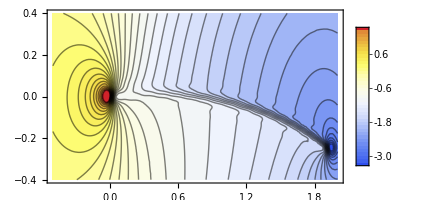

```mathematica
Show[Quiet@ContourPlot[PressureCoefficient[x,y],{x,-0.5,2},{y,-0.4,0.4},AspectRatio->Automatic,PlotRangePadding->None,ColorFunction->"TemperatureMap",Contours->40,PlotLegends->Automatic,PlotRange->All,ImageSize->Medium],Graphics[{FaceForm[White],EdgeForm[Black]}]]
```

```mathematica
ResourceFunction["ComputationalEssayTemplate"][]
```